## Packages loading and nb definitions

```mathematica
SetDirectory[NotebookDirectory[]];
Get["../Mathematica_packages/"<>#]&/@{"Chaometer.wl","QMB.wl"};
```

```mathematica
(* Canal completamente depolarizante que actúa sobre el primer espín de una cadena de N espines *)
DepolarizingChannel[ρ_,L_]:=
Module[{kraus},
(* Construir operadores de Kraus *)
kraus=KroneckerProduct[#,IdentityMatrix[2^(L-1)]]&/@ArrayReshape[IdentityMatrix[4]/√2,{4,2,2}];

(* Aplicar canal en su forma de Kraus a ρ *)
Total[#.ρ.ConjugateTranspose[#]&/@kraus]
]
```

## Parameters setup

```mathematica
L=11(*number of spins*);
{hx,hz,J}={1.,0.5,ConstantArray[1.,L-1]}(*hz=0.5 chaotic, hz=2.5 regular*)
```

{1.,0.5,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvalsH,eigenvecsH}=N[Chop[Eigensystem[H]]];
]
```

```mathematica
(*Three initial random states of the environment Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
SeedRandom[32371];
ψ0E=Table[RandomChainProductState[L-1],3];
```

```mathematica
superoperators=ToExpression[Import["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/chaotic/superoperators_2.csv"][[2;;]](*la primera fila tiene la info*)];
```

```mathematica
(* Check de que un superoperador random sea el correcto comparando con la construccion de alguno  *)
t=RandomChoice[Range[0,50,0.1]](* un tiempo aleatorio *);
MatrixForm[Round[#,10.^-7]]&/@{Chop@Superoperator[t,ψ0E[[2]](*número de estado aleatorio*),eigenvalsH,eigenvecsH,L],superoperators[[t/0.1+1]]}
Equal@@%
```

{(0.493083 | 0.0122412+0.0119287 ⅈ | 0.0122412-0.0119287 ⅈ | 0.475635
0.0182229+0.0081882 ⅈ | 0.0410292-0.006847 ⅈ | 0.0367151+0.0005877 ⅈ | -0.0344784+0.0009147 ⅈ
0.0182229-0.0081882 ⅈ | 0.0367151-0.0005877 ⅈ | 0.0410292+0.006847 ⅈ | -0.0344784-0.0009147 ⅈ
0.506917 | -0.0122412-0.0119287 ⅈ | -0.0122412+0.0119287 ⅈ | 0.524365),(0.493083 | 0.0122412+0.0119287 ⅈ | 0.0122412-0.0119287 ⅈ | 0.475635
0.0182229+0.0081882 ⅈ | 0.0410292-0.006847 ⅈ | 0.0367151+0.0005877 ⅈ | -0.0344784+0.0009147 ⅈ
0.0182229-0.0081882 ⅈ | 0.0367151-0.0005877 ⅈ | 0.0410292+0.006847 ⅈ | -0.0344784-0.0009147 ⅈ
0.506917 | -0.0122412-0.0119287 ⅈ | -0.0122412+0.0119287 ⅈ | 0.524365)}

True

```mathematica
chois=1/2*Reshuffle/@superoperators;
```

```mathematica
choiPurities=Transpose[{Range[0,50,0.1],Chop[Purity/@chois]}];
```

## Choi matrix

```mathematica
MatrixForm@Table[
{q,r}=IntegerDigits[i,2,2]+1;{p,s}=IntegerDigits[j,2,2]+1;
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{s-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,q}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{r-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]/2
,{i,0,3},{j,0,3}]
```

(0.246192+0. ⅈ | 0.0154966+0.00356999 ⅈ | -0.000178027-0.00466358 ⅈ | 0.00614217+0.00118478 ⅈ
0.0154966-0.00356999 ⅈ | 0.246958+0. ⅈ | 0.0100395+0.00520072 ⅈ | -0.022327-0.00607428 ⅈ
-0.000178027+0.00466358 ⅈ | 0.0100395-0.00520072 ⅈ | 0.253808+0. ⅈ | -0.0154966-0.00356999 ⅈ
0.00614217-0.00118478 ⅈ | -0.022327+0.00607428 ⅈ | -0.0154966+0.00356999 ⅈ | 0.253042+0. ⅈ)

```mathematica
MatrixForm[chois[[t/0.1+1]]]
```

(0.246192 | 0.0154966+0.00356999 ⅈ | -0.000178027-0.00466358 ⅈ | 0.00614217+0.00118478 ⅈ
0.0154966-0.00356999 ⅈ | 0.246958 | 0.0100395+0.00520072 ⅈ | -0.022327-0.00607428 ⅈ
-0.000178027+0.00466358 ⅈ | 0.0100395-0.00520072 ⅈ | 0.253808 | -0.0154966-0.00356999 ⅈ
0.00614217-0.00118478 ⅈ | -0.022327+0.00607428 ⅈ | -0.0154966+0.00356999 ⅈ | 0.253042)

## Analytic purities expressions

```mathematica
t=RandomChoice[Range[0,50,0.1]](* un tiempo aleatorio *)
```

46.6

```mathematica
(*  Calcular {pureza numérica, pureza analítica con eq:choi:chaometer:purity:1} *)
{Select[choiPurities,#[[1]]==t&],Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,q}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2/4
,{i,2},{j,2},{p,2},{q,2}]}
```

{{{46.6,0.253144}},0.253144}

```mathematica
(* Calcular la pureza analítica con eq:choi:chaometer:purity:2, echo de Loshcmidt *)
ψ1=StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{#}],ψ0E[[2]]],eigenvalsH,eigenvecsH]&/@{0,1};
ρ1=Total[Dyad[#]&/@ψ1]/2;(* U (I/2 ⊗ ψψ) U^† *)
ρ2=DepolarizingChannel[ρ1,L];
Chop@Total[Braket[#,ρ2.#]&/@ψ1]
```

0.253144

### eq:appendix:A:1

```mathematica
(* Calcular el primer término dentro del paréntesis de eq:appendix:A:1 *)
t1=Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,p}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2
,{i,2},{j,2},{p,2}]
```

1.00299

```mathematica
(* Calcular el segundo término dentro del paréntesis de eq:appendix:A:1 *)
t2=Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,Mod[p+1,2,1]}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2
,{i,2},{j,2},{p,2}]
```

0.00958805

```mathematica
{Select[choiPurities,#[[1]]==t&],(t1+t2)/4}
```

{{{46.6,0.253144}},0.253144}

### eq:appendix:A:2

```mathematica
(* Calcular el primer término dentro del paréntesis de eq:appendix:A:2 para confirmar que es igual a 2 *)
t1=Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2
,{i,2},{j,2}]
```

2.

```mathematica
(* Calcular la suma de los primeros dos términos dentro del paréntesis de eq:appendix:A:2. Debería ser igual al primer término de eq:appendix:A:1 *)
t2=-2*Sum[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{1,1}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]*Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{2,2}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]
,{i,2},{j,2}]
```

-0.997013+0. ⅈ

```mathematica
(* Calcular el tercer término dentro del paréntesis de eq:appendix:A:2 *)
t3=Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,Mod[p+1,2,1]}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2
,{i,2},{j,2},{p,2}]
```

0.00958805

```mathematica
{Select[choiPurities,#[[1]]==t&],(t1+t2+t3)/4}
```

{{{46.6,0.253144}},0.253144+0. ⅈ}

## Purity worked more

```mathematica
(* primer término de la pureza analítica *)
Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,p}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2/4
,{i,2},{j,2},{p,2}]
```

0.250966

```mathematica
(* primer término de la pureza analítica *)
Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].IdentityMatrix[2^L].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]
]^2/4
,{i,2},{j,2}]
```

0.5

```mathematica
t=1.2
```

1.2

```mathematica
(* segundo término de la pureza analítica *)
-Sum[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{1,1}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]*Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{2,2}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]
,{i,2},{j,2}]/2
```

-0.219887+0. ⅈ

```mathematica
0.5+%37
```

0.250603+0. ⅈ

```mathematica
Times@@Chop[(superoperators[[0.6/0.1+1]].{1/2,0,0,1/2})[[{1,4}]]]
```

0.249998

## Choi’s purity of a Hamiltonian from GOE

```mathematica
Module[{H},
H=RandomVariate[GaussianOrthogonalMatrixDistribution[2^L]];
{eigenvalsH,eigenvecsH}=N[Chop[Eigensystem[H]]];
]
```

```mathematica
t=0.01;
```

```mathematica
(*pureza matriz de Choi*)
Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,q}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2/4
,{i,2},{j,2},{p,2},{q,2}]
```

0.861003

```mathematica
(*segundo término pureza matriz de Choi *)
-Sum[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{1,1}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]*Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{2,2}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]
,{i,2},{j,2}]/2
```

-0.249623+0. ⅈ

```mathematica
(*tercer término pureza matriz de Choi *)
Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,Mod[p+1,2,1]}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2/4
,{i,2},{j,2},{p,2}]
```

0.000355922

```mathematica
0.5+%90+%91
```

0.250287+0. ⅈ

## Pureza con Hamiltoniano GOE, aquí estoy ahorita

```mathematica
L=10;
```

```mathematica
(* Calcular un Hamiltoniano de GOE y obtener sus eigenvalores y eigenvectores *)
Module[{H},
H=RandomVariate[GaussianOrthogonalMatrixDistribution[2^L]];
(*U=MatrixExp[-I H];*)
{eigenvalsH,eigenvecsH}=Chop[Eigensystem[H]];
]
```

```mathematica
(* Revisar que los eigenvectores esten normalizados *)
AllTrue[Norm/@eigenvecsH,#==1.&]
```

True

```mathematica
(* Definir un estado inicial para el entorno de L-1 espines *)
ψ0E=RandomChainProductState[L-1];
```

```mathematica
(* Calcular el segundo término dentro del paréntesis de eq:appendix:A:2 *)
Sum[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{1,1}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E],eigenvalsH,eigenvecsH]*Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{2,2}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E],eigenvalsH,eigenvecsH]
,{i,2},{j,2}]
```

0.498268+0. ⅈ

```mathematica
(*tercer término pureza matriz de Choi *)
Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,Mod[p+1,2,1]}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E],eigenvalsH,eigenvecsH]]^2/4
,{i,2},{j,2},{p,2}]
```

0.000410383

## Poisson random matrix

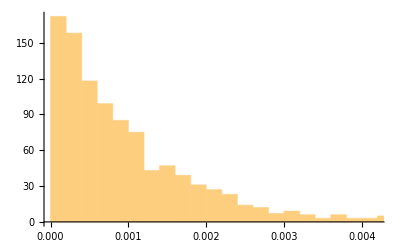

```mathematica
(*Set the size of the matrix*)n=1000;

(*Create a diagonal matrix with uniformly distributed random entries*)
d=DiagonalMatrix[RandomReal[{0,1},n]];

(*Optionally,apply a random unitary transformation*)
A=RandomComplex[{-1,1},{n,n}]; (*Generate a random complex matrix*)
{U,R}=QRDecomposition[A];
RandomMatrix=Transpose[U].d.U;

(*Get the eigenvalues*)
eigenvalues=Eigenvalues[RandomMatrix];

(*Plot the level spacing distribution*)
Histogram[Differences[Sort[Chop@eigenvalues]]]
```

```mathematica
Sort[Diagonal[d]]==Chop[Sort[eigenvalues]]
```

False

```mathematica
Sort[Diagonal[d]][[;;10]]
```

{0.00074799,0.00090323,0.00169657,0.00173701,0.00181221,0.00218115,0.00248423,0.00352086,0.00563544,0.00649427}

```mathematica
Chop[Sort[eigenvalues][[;;10]]]
```

{0.00074799,0.00090323,0.00169657,0.00173701,0.00181221,0.00218115,0.00248423,0.00352086,0.00563544,0.00649427}